{μ→206.183,σ→60.0106,k→707474.}

141.314

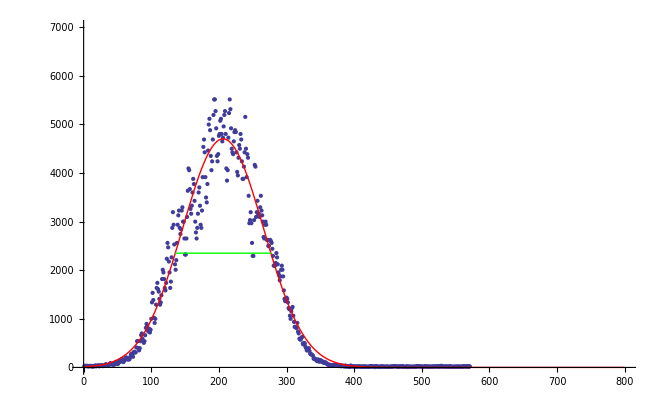

```mathematica
rawData = Import[NotebookDirectory[]<>"88cm_y.dat"];
messData = ToExpression[rawData];
Clear @ model;
model[x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));
param=FindFit[messData, model[x], {{μ, 350}, {σ, 7000}, {k, 100000}}, x]
FWHM = 2*Sqrt[2 Log[2]] * σ /. param
Peak = k*1/(σ*Sqrt[2*Pi]) /.param;
Show[{ListPlot[messData, PlotRange->{{0,800}, {0, 7000}}], Plot[ model[x]/.param,  {x,0,800}, PlotStyle->Red, PlotRange->{{0,800}, {0, 7000}}], Graphics[{Green, Line[{{μ-FWHM/2, Peak/2}/. param,{μ+FWHM/2, Peak/2}/. param}]}]}]
```